```mathematica
Clear["Global`*"];
SetDirectory[NotebookDirectory[]]; 
Needs["ErrorBarPlots`"];
Needs["NumericalCalculus`"];
```

### Lattice data (Parametrized)

```mathematica
a00=7.53891;a10=−6.18858;a20=−5.37961;a30=7.08750;a40=−0.977970 ;a50=0.0302636;
b00=2.24530;b10=−6.02568;b20=15.3737;b30=−19.6331;b40=10.2400;b50=0.799479;

a04= 0.0033478751744618696;a14 = -0.023630865535170107;a24=0.06572603857913838;a34 = -0.08929058193709703;a44 = 0.06229229147536862;
a54 =-0.02149054884376173;a64 = 0.003183415072583582;a74 = -0.00012946871100831444;b04 = 0.267850013328013;b14 = -2.106985569069408;
b24 = 6.50705446533695;b34 = -9.553392725616968; b44 = 6.020899520992443;b54 = 0.20838912353460728;b64 = -2.0311458080878224;
 b74 = 0.6874559629219487;

h1 = -0.318451210804933;h2=0.4927954599817167;f3 = 0.14931911904005374;f4 = 6.6991991785479295;f5 = -5.110080379554422;

(*Subscript[χ, 0](T) from lattice*)
chi0[T_]:=(a00+a10*(154/T)+a20*(154/T)^2+a30*(154/T)^3+a40*(154/T)^4+a50*(154/T)^5)/(b00+b10*(154/T)+b20*(154/T)^2+b30*(154/T)^3+b40*(154/T)^4+b50*(154/T)^5);
(*Subscript[χ, 2](T) from lattice*)
chi2n[T_]:=Exp[-h1/(T/200)  -h2/(T/200)^2]*f3*(1+Tanh[(f4*(T/200)+f5)]);
(*Subscript[χ, 4](T) from lattice*)
chi4[T_]:=(a04+a14*(154/T)+a24*(154/T)^2+a34*(154/T)^3+a44*(154/T)^4+a54*(154/T)^5+a64*(154/T)^6+a74*(154/T)^7)/(b04+b14*(154/T)+b24*(154/T)^2+b34*(154/T)^3+b44*(154/T)^4+b54*(154/T)^5+b64*(154/T)^6+b74*(154/T)^7);
dchi2dT[T_]:=1/200 ⅇ^(-(40000*h2)/T^2-(200*h1)/T) f3* f4*Sech[f5+(f4*T)/200]^2+ⅇ^(-(40000*h2)/T^2-(200*h1)/T) *f3*((80000*h2)/T^3+(200*h1)/T^2) (1+Tanh[f5+(f4*T)/200]);
```

### Kappa2 (Parametrized)

```mathematica
Kappa2La = Import["/Users/michaeladmin/Desktop/HRG-AltExS/Lattice/2102.06660/kappa_all.dat"];
Kappa2Lat = Table[{Kappa2La[[i,1]],Kappa2La[[i,2]],Kappa2La[[i,3]],Kappa2La[[i,4]],Kappa2La[[i,5]]},{i,2,Length[Kappa2La]}];
```

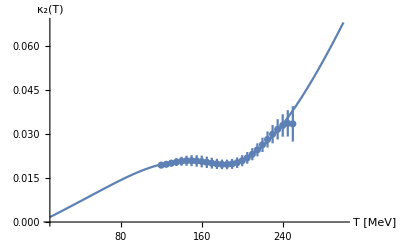

```mathematica
a0x=-0.005962695041907612;a1x=2.4311870267845297;a2x=-4.470657283293225;a3x=3.35533046923378;a4x=-2.1650786307325816;
a5x=1.1997134556608198;
b0x=69.70395579728883;
b1x=-137.83151716912178;
b2x=103.36622431692021;
b3x=-27.387528625996183;
b4x=8.464555186514893;
b5x=-0.1422975425743732;
Kappa2n[T_]:=(a0x+a1x/(200/T)+a2x/(200/T)^2+a3x/(200/T)^3+a4x/(200/T)^4+a5x/(200/T)^5)/(b0x+b1x/(200/T)+b2x/(200/T)^2+b3x/(200/T)^3+b4x/(200/T)^4+b5x/(200/T)^5);

dKappa2ndT[T_]:=-((b1x/200+(b2x T)/20000+(3 b3x T^2)/8000000+(b4x T^3)/400000000+(b5x T^4)/64000000000) (a0x+(a1x T)/200+(a2x T^2)/40000+(a3x T^3)/8000000+(a4x T^4)/1600000000+(a5x T^5)/320000000000))/((b0x+(b1x T)/200+(b2x T^2)/40000+(b3x T^3)/8000000+(b4x T^4)/1600000000+(b5x T^5)/320000000000)^2)+(a1x/200+(a2x T)/20000+(3 a3x T^2)/8000000+(a4x T^3)/400000000+(a5x T^4)/64000000000)/(b0x+(b1x T)/200+(b2x T^2)/40000+(b3x T^3)/8000000+(b4x T^4)/1600000000+(b5x T^5)/320000000000);
Show[Plot[Kappa2n[T],{T,10,300},AxesLabel->{ "T [MeV]", "κ_2(T)"},LabelStyle->{Black,Bold,25}],ErrorListPlot[Kappa2Lat[[All,{1,2,3}]]]]
```

### Ising Scaling (R,θ) -> (r,h)

```mathematica
a=-0.76201;
b=0.00804;
htild[theta_]:=theta*(1+a*theta^2+b*theta^4);
alpha=0.11;
beta=0.326;
c0=beta/(2-alpha)*(1+a+b);
c1=-1/2*1/(alpha-1)*((1-2*beta)*(1+a+b)-2*beta*(a+2*b)); 
c2=-1/(2*alpha)*(2*beta*b-(1-2*beta)*(a+2*b));
c3=-1/(2*(alpha+1))*b*(1-2beta);
g[theta_]:=c0+c1*(1-theta^2)+c2*(1-theta^2)^2+c3*(1-theta^2)^3;

h0=0.394;
M0=0.605;
delta=4.8;
bede = beta*delta;
h[R_,theta_]:=h0*R^(beta*delta)*htild[theta];
r[R_,theta_]:=R*(1-theta^2);

PIsing1[R_,theta_]:=h0*M0*R^(2-alpha)*(theta*htild[theta]-g[theta]);

M[xh_,xr_]:=FindRoot[{h[R,theta]==  xh&&r[R,theta]==xr },{{R,√(xh^2+xr^2)},{theta,Sign[xh]}}] 

thetax[xr_,xh_]:=M[xh,xr][[2,2]]
RRx[xr_,xh_]:=M[xh,xr][[1,2]]
Pt[xr_,xh_]:=PIsing1[RRx[xr,xh],thetax[xr,xh]]
{Plot3D[thetax[xr,xh],{xr,-10,10},{xh,-10,10}, AxesLabel->{"r", "h", "θ(r,h)"},LabelStyle->{Black,Bold,25}],Plot3D[RRx[xr,xh],{xr,-10,10},{xh,-10,10}, AxesLabel->{"r", "h", "R(r,h)"},LabelStyle->{Black,Bold,25}]}
```

{-Graphics3D-,-Graphics3D-}

### Mapping (r,h) -> (T,μ_B)

```mathematica
ρ =5; muBC = 350.0;T0 = 158.0; angle12 =π/180*5; w = 20.0; (*Free parameters ρ, Subscript[μ, B], Subscript[α, 12], w*)
hh[tprime_,muB_]:=-(tprime - T0)/(w*T0*Sin[angle12]);
dhhdmuB[T_,muB_] := -1/(w*T0*Sin[angle12])*dTprimedmuB[T,muB];
d2hhdmuB2[T_,muB_] := -1/(w*T0*Sin[angle12])*d2TprimedmuB2[T,muB];
rr[tprime_,muB_]:=-1/ρ((muB^2 - muBC^2)/(T0^2*(2*muBC/T0)*w) +hh[tprime,muB]/1*Cos[angle12]);
drrdmuB[T_,muB_]:= -1/ρ*((2*muB)/(T0^2*(2*muBC/T0)*w)+dhhdmuB[T,muB]/1 *Cos[angle12]);
d2rrdmuB2[T_,muB_]:= -1/ρ*(2/(T0^2*(2*muBC/T0)*w)+d2hhdmuB2[T,muB]/1 *Cos[angle12]);
Tprime[T_,muB_]:=T(1+Kappa2n[T]*(muB/T)^2);
dTprimedT[T_,muB_]:=1+dKappa2ndT[T]*muB^2/T-Kappa2n[T]*(muB/T)^2

dTprimedmuB[T_,muB_]:=2*Kappa2n[T]*(muB/T);
d2TprimedmuB2[T_,muB_]:=2*Kappa2n[T]*(1/T);

TC[muB_] :=FindRoot[{T0 -Tprime[T,muB]},{T,5}][[1,2]]
```

```mathematica
thetaxx[T_,muB_]:=thetax[rr[Tprime[T,muB],muB],hh[Tprime[T,muB],muB]];
RRxx[T_,muB_]:=RRx[rr[Tprime[T,muB],muB],hh[Tprime[T,muB],muB]];
```

```mathematica
P[T_,muB_]:=PIsing1[RRxx[T,muB],thetaxx[T,muB]];
```

```mathematica
Plot3D[P[T,muB],{T,10,400},{muB,0,700}]
```

-Graphics3D-

### Derivatives with respect to muB

```mathematica
(*g(theta) and derivatives*)
g[theta_]:=c0+c1*(1-theta^2)+c2*(1-theta^2)^2+c3*(1-theta^2)^3;
dgdth[theta_]:=-2*theta*(c1+(-1+theta^2)*(-2*c2+3*c3*(-1+theta^2)));
d2gdth2[theta_]:=-2*(c1+c2*(2-6*theta^2)+3*c3*(1-6*theta^2+5*theta^4));

(*htilda(theta) and derivatives*)
htild[theta_]:=theta*(1+a*theta^2+b*theta^4);
dhtilddth[theta_]:=1+3*a*theta^2+5*b*theta^4;
d2htilddth2[theta_]:=6*a*theta+20*b*theta^3;


(*Pressure in (R,theta)*)
Press[R_,theta_]:=h0*M0*R^(2-alpha)*(theta*htild[theta]-g[theta]);

(*1st derivative of pressure wrt to R and theta*)
dPdR[R_,theta_]:=(2-alpha)*h0*M0*(-g[theta]+theta*htild[theta])*R^(1-alpha);
dPdth[R_,theta_]:=h0*M0*(-dgdth[theta]+theta*dhtilddth[theta]+htild[theta])*R^(2-alpha);

(*2nd derivative of pressure wrt to R and theta*)
d2PdR2[R_,theta_]:=(1-alpha)*(2-alpha)*h0*M0*(-g[theta]+theta*htild[theta])*R^(-alpha);
d2PdRdth[R_,theta_]:=(2-alpha)*h0*M0*(-dgdth[theta]+theta*dhtilddth[theta]+htild[theta])*R^(1-alpha);
d2Pdth2[R_,theta_]:=h0*M0*(-d2gdth2[theta]+theta*d2htilddth2[theta]+2*dhtilddth[theta])*R^(2-alpha);

dRdrr[R_,theta_]:=dhtilddth[theta]*Power[dhtilddth[theta]+2*bede*theta*htild[theta]-dhtilddth[theta]*Power[theta,2],-1];
dRdh[R_,theta_]:=2*theta*Power[h0,-1]*Power[R,1-bede]*Power[dhtilddth[theta]+2*bede*theta*htild[theta]-dhtilddth[theta]*Power[theta,2],-1];
dthdrr[R_,theta_]:=bede*htild[theta]*Power[R,-1]*Power[-2*bede*theta*htild[theta]+dhtilddth[theta]*(-1+Power[theta,2]),-1];
dthdh[R_,theta_]:=Power[h0,-1]*Power[R,-(bede)]*(-1+Power[theta,2])*Power[-2*bede*theta*htild[theta]+dhtilddth[theta]*(-1+Power[theta,2]),-1];

d2PdR2[R_,theta_]:=(1-alpha)*(2-alpha)*h0*M0*(-g[theta]+theta*htild[theta])*R^(-alpha);
d2PdRdth[R_,theta_]:=(2-alpha)*h0*M0*(-dgdth[theta]+theta*dhtilddth[theta]+htild[theta])*R^(1-alpha);
d2Pdth2[R_,theta_]:=h0*M0*(-d2gdth2[theta]+theta*d2htilddth2[theta]+2*dhtilddth[theta])*R^(2-alpha);
```

```mathematica
dRdrr[R_,theta_]:=dhtilddth[theta]*(dhtilddth[theta]+2*bede*theta*htild[theta]-dhtilddth[theta]*theta^2)^(-1);
dRdh[R_,theta_]:=2*theta/h0*R^(1-bede)*(dhtilddth[theta]+2*bede*theta*htild[theta]-dhtilddth[theta]*theta^2)^(-1);
dthdrr[R_,theta_]:=bede*htild[theta]*R^(-1)*(-2*bede*theta*htild[theta]+dhtilddth[theta]*(-1+theta^2))^(-1);
dthdh[R_,theta_]:=1/h0*R^(-bede)*(-1+theta^2)*(-2*bede*theta*htild[theta]+dhtilddth[theta]*(-1+theta^2))^(-1);
```

```mathematica
d2Rdrr2[R_,theta_]:=-(dhtilddth[theta]*(-2*theta*dhtilddth[theta]*dthdrr[R,theta]+2*beta*delta*theta*dhtilddth[theta]*dthdrr[R,theta]+2*beta*delta*dthdrr[R,theta]*htild[theta]+d2htilddth2[theta]*dthdrr[R,theta]*(1-theta^2))*(2*beta*delta*theta*htild[theta]+dhtilddth[theta]*(1-theta^2))^(-2))+d2htilddth2[theta]*dthdrr[R,theta]*(2*beta*delta*theta*htild[theta]+dhtilddth[theta]*(1-theta^2))^(-1);
d2Rdh2[R_,theta_]:=-2*theta*(h0^(-1))*(R^(1-beta*delta))*(d2htilddth2[theta]*dthdh[R,theta]-2*theta*dhtilddth[theta]*dthdh[R,theta]+2*beta*delta*theta*dhtilddth[theta]*dthdh[R,theta]+2*beta*delta*dthdh[R,theta]*htild[theta]-d2htilddth2[theta]*dthdh[R,theta]*(theta^2))*(dhtilddth[theta]+2*beta*delta*theta*htild[theta]-dhtilddth[theta]*(theta^2))^(-2)+2*(1-beta*delta)*theta*dRdh[R,theta]*(h0^(-1))*(R^(-beta*delta))*((dhtilddth[theta]+2*beta*delta*theta*htild[theta]-dhtilddth[theta]*(theta^2))^(-1))+2*dthdh[R,theta]*(h0^(-1))*(R^(1-beta*delta))*((dhtilddth[theta]+2*beta*delta*theta*htild[theta]-dhtilddth[theta]*(theta^2))^(-1));
d2thdrr2[R_,theta_]:=beta*delta*htild[theta]*(R^(-1))*(-2*theta*dhtilddth[theta]*dthdrr[R,theta]+2*beta*delta*theta*dhtilddth[theta]*dthdrr[R,theta]+2*beta*delta*dthdrr[R,theta]*htild[theta]+d2htilddth2[theta]*dthdrr[R,theta]*(1-(theta^2)))*(2*beta*delta*theta*htild[theta]+dhtilddth[theta]*(1-(theta^2)))^(-2)+beta*delta*dRdrr[R,theta]*htild[theta]*(R^(-2))*(2*beta*delta*theta*htild[theta]+dhtilddth[theta]*(1-(theta^2)))^(-1)-beta*delta*dhtilddth[theta]*dthdrr[R,theta]*(R^(-1))*(2*beta*delta*theta*htild[theta]+dhtilddth[theta]*(1-(theta^2)))^(-1);
d2thdh2[R_,theta_]:=-(h0^(-1))*R^(-beta*delta)*(-2*theta*dhtilddth[theta]*dthdh[R,theta]+2*beta*delta*theta*dhtilddth[theta]*dthdh[R,theta]+2*beta*delta*dthdh[R,theta]*htild[theta]+d2htilddth2[theta]*dthdh[R,theta]*(1-(theta^2)))*(1-(theta^2))*(2*beta*delta*theta*htild[theta]+dhtilddth[theta]*(1-(theta^2)))^(-2)-2*theta*dthdh[R,theta]*(h0^(-1))*R^(-(beta*delta))*(2*beta*delta*theta*htild[theta]+dhtilddth[theta]*(1-(theta^2)))^(-1)-beta*delta*dRdh[R,theta]*(h0^(-1))*R^(-1-beta*delta)*(1-(theta^2))*(2*beta*delta*theta*htild[theta]+dhtilddth[theta]*(1-(theta^2)))^(-1);

d2Rdrrdh[R_,theta_]:=-(dhtilddth[theta]*(-2*theta*dhtilddth[theta]*dthdh[R,theta]+2*beta*delta*theta*dhtilddth[theta]*dthdh[R,theta]+2*beta*delta*dthdh[R,theta]*htild[theta]+d2htilddth2[theta]*dthdh[R,theta]*(1-(theta^2)))*(2*beta*delta*theta*htild[theta]+dhtilddth[theta]*(1-(theta^2)))^(-2))+d2htilddth2[theta]*dthdh[R,theta]*(2*beta*delta*theta*htild[theta]+dhtilddth[theta]*(1-(theta^2)))^(-1);

d2thdrrdh[R_,theta_]:=beta*delta*R^-2*(htild[theta]*(2*beta*delta*(theta*dRdh[R,theta]+R*dthdh[R,theta])*htild[theta]-R*d2htilddth2[theta]*dthdh[R,theta]*(-1+theta^2))+dhtilddth[theta]*(htild[theta]*(-2*R*theta*dthdh[R,theta]-dRdh[R,theta]*(-1+theta^2))+R*dhtilddth[theta]*dthdh[R,theta]*(-1+theta^2)))*(-2*beta*delta*theta*htild[theta]+dhtilddth[theta]*(-1+theta^2))^-2;
```

```mathematica
(*derivative of pressure wrt to r and h *)
dPdrr[R_,theta_]:=dPdR[R,theta]*dRdrr[R,theta]+dPdth[R,theta]*dthdrr[R,theta];
dPdh[R_,theta_]:=dPdR[R,theta]*dRdh[R,theta]+dPdth[R,theta]*dthdh[R,theta];
d2Pdrr2[R_,theta_]:=d2Rdrr2[R,theta]*dPdR[R,theta]+d2thdrr2[R,theta]*dPdth[R,theta]+2*d2PdRdth[R,theta]*dRdrr[R,theta]*dthdrr[R,theta]+d2PdR2[R,theta]*(dRdrr[R,theta])^2+d2Pdth2[R,theta]*(dthdrr[R,theta])^2;
d2Pdh2[R_,theta_]:=d2Rdh2[R,theta]*dPdR[R,theta]+d2thdh2[R,theta]*dPdth[R,theta]+2*d2PdRdth[R,theta]*dRdh[R,theta]*dthdh[R,theta]+d2PdR2[R,theta]*(dRdh[R,theta])^2+d2Pdth2[R,theta]*(dthdh[R,theta])^2;
d2Pdrrdh[R_,theta_]:=d2Rdrrdh[R,theta]*dPdR[R,theta]+d2thdrrdh[R,theta]*dPdth[R,theta]+d2PdR2[R,theta]*dRdh[R,theta]*dRdrr[R,theta]+d2PdRdth[R,theta]*dRdrr[R,theta]*dthdh[R,theta]+d2PdRdth[R,theta]*dRdh[R,theta]*dthdrr[R,theta]+d2Pdth2[R,theta]*dthdh[R,theta]*dthdrr[R,theta];
```

```mathematica
(*derivative of pressure wrt to muB *)
dPdmuB[T_,muB_,R_,theta_]:=dhhdmuB[T,muB]*dPdh[R,theta]+dPdrr[R,theta]*drrdmuB[T,muB];
d2PdmuB2[T_,muB_,R_,theta_]:=d2Pdh2[R,theta]*Power[dhhdmuB[T,muB],2]+d2hhdmuB2[T,muB]*dPdh[R,theta]+d2rrdmuB2[T,muB]*dPdrr[R,theta]+2*d2Pdrrdh[R,theta]*dhhdmuB[T,muB]*drrdmuB[T,muB]+d2Pdrr2[R,theta]*Power[drrdmuB[T,muB],2];
```

```mathematica
(*Ising Pressure in terms of T, Subscript[μ, B] and its derivatives wrt to muB *)
Pcrit[T_,muB_]:=Press[RRxx[T,muB],thetaxx[T,muB]]
BardIsingA[T_,muB_]:=T*dPdmuB[T,muB,RRxx[T,muB],thetaxx[T,muB]]
dBardIsingdmuBA[T_,muB_]:=T*T*d2PdmuB2[T,muB,RRxx[T,muB],thetaxx[T,muB]]
```

#### Regular function F(T,μ_B)

```mathematica
(*Regular function  in terms of T, Subscript[μ, B] and its derivative wrt to muB *)
Fnregular[T_,muB_]:=(muB/muBC)^6*(T/TC[muB])^2
dFnregulardmuB[T_,muB_]:=6*muB^5/muBC^6*(T/TC[muB])^2

(*The Critical temperature  and its derivatives*)
Tcrit[T_,muB_]:=If[muB==0,T0,T0+(1/dchi2dT[T0])*BardIsingA[T,muB]/(muB/T)*Fnregular[T,muB]]
diff=0.01;
dTcritdmuBn[T_,muB_]:=T*(Tcrit[T,muB-2*diff]-8*Tcrit[T,muB-diff]+8*Tcrit[T,muB+diff]-Tcrit[T,muB+2*diff])/(12*diff)
dTcritdmuB[T_,muB_]:=If[muB==0,0,(1/dchi2dT[T0])*((dBardIsingdmuBA[T,muB]/(muB/T)-BardIsingA[T,muB]/(muB/T)^2)*Fnregular[T,muB]+(BardIsingA[T,muB]/(muB/T))*T*dFnregulardmuB[T,muB])]
dTcritdT[T_,muB_]:=(Tcrit[T-2*diff,muB]-8*Tcrit[T-diff,muB]+8*Tcrit[T+diff,muB]-Tcrit[T+2*diff,muB])/(12*diff)
```

Tfull (T, μ_B)

```mathematica
(*Total Temperature Tfull constains lattice merged with Ising *)
Tfull[T_,muB_]:=Tprime[T,muB]+Tcrit[T,muB]-T0
```

### Thermodynamics

#### Baryon density

```mathematica
nBfull[T_,muB_]:=muB/T*chi2n[Tfull[T,muB]]*T^3
Plot3D[nBfull[T,muB]/T^3,{muB,0,700},{T,10,400},AxesLabel->{"μ_B [MeV] ", "T [MeV]", "n_B/T^3"},LabelStyle->{Black,Bold,25}]
```

-Graphics3D-

#### Baryon Susceptibility χ_2

```mathematica
chi2full[T_,muB_]:=T^2*(chi2n[Tfull[T,muB]]+muB*dchi2dT[Tfull[T,muB]]*(dTprimedmuB[T,muB]+dTcritdmuB[T,muB]/T))
Plot3D[chi2full[T,muB]/T^2,{muB,0,700},{T,10,400},AxesLabel->{"μ_B [MeV] ", "T [MeV]", "χ_2/T^2"},LabelStyle->{Black,Bold,25}]
```

-Graphics3D-

```mathematica
dnBdT[T_,muB_]:=muB*T*(2*chi2n[Tfull[T,muB]]+T*dchi2dT[Tfull[T,muB]]*(dTprimedT[T,muB]+dTcritdT[T,muB]))
```

#### Pressure

```mathematica
Pressfull[T_,muB_]:=Module[{integral,y,step=1,values},integral=0.0;
values={nBfull[T,0]};(*Store initial value*)Do[AppendTo[values,nBfull[T,y]];
integral+=(values[[-1]]+values[[-2]])*step/2.0,{y,step,muB,step}];
T^4*chi0[T]+integral]
```

```mathematica
Plot3D[Pressfull[T,muB]/T^4,{muB,0,700},{T,10,400},AxesLabel->{"μ_B [MeV] ", "T [MeV]", "P/T^4"},LabelStyle->{Black,Bold,25}]
```

-Graphics3D-

#### Entropy

```mathematica
Entrpy[T_,muB_]:=(Pressfull[T-2*diff,muB]-8*Pressfull[T-diff,muB]+8*Pressfull[T+diff,muB]-Pressfull[T+2*diff,muB])/(12*diff)
dEntrpydT[T_,muB_]:=(-Pressfull[T-2*diff,muB]+16*Pressfull[T-diff,muB]-30*Pressfull[T,muB]+16*Pressfull[T+diff,muB]-Pressfull[T+2*diff,muB])/(12*diff^2)
```

```mathematica
Plot3D[Entrpy[T,muB]/T^3,{muB,0,700},{T,10,400},AxesLabel->{"μ_B [MeV] ", "T [MeV]", "S(T,μ_B)"},LabelStyle->{Black,Bold,25}]
```

-Graphics3D-

#### Energy

```mathematica
Energy[T_,muB_]:=-Pressfull[T,muB]+T*Entrpy[T,muB]+muB*nBfull[T,muB]
Plot3D[Energy[T,muB]/T^4,{muB,0,700},{T,10,400},AxesLabel->{"μ_B [MeV] ", "T [MeV]", "ϵ(T,μ_B)"},LabelStyle->{Black,Bold,25}]
```

-Graphics3D-

#### Cv (Specific heat capacity at constant volume)

```mathematica
Cv[T_,muB_]:=T*(dEntrpydT[T,muB]*chi2fulln[T,muB]-dnBdT[T,muB]*dnBdT[T,muB])/chi2fulln[T,muB]
Plot3D[Cv[T,muB]/T^2,{muB,0,700},{T,10,400},AxesLabel->{"μ_B [MeV] ", "T [MeV]", "Cv(T,μ_B)"},LabelStyle->{Black,Bold,25}]
```

$Aborted

#### Speed of Sound

```mathematica
Cs2[T_,muB_]:=(nBfull[T,muB]^2*dEntrpydT[T,muB]-2*Entrpy[T,muB]*nBfull[T,muB]*dnBdT[T,muB]+Entrpy[T,muB]^2*chi2fulln[T,muB])/((Energy[T,muB]+Pressfull[T,muB])*(dEntrpydT[T,muB]*chi2fulln[T,muB]-dnBdT[T,muB]^2));
Plot3D[Cs2[T,muB]/T^2,{muB,0,700},{T,10,400},AxesLabel->{"μ_B [MeV] ", "T [MeV]", "C_s^2(T,μ_B)"},LabelStyle->{Black,Bold,25}]
```